```mathematica
FoldList[Product,Table[i,{i,1,8}]]
```

{1,1,1,1,1,1,1,1}

```mathematica
a=Table[i,{i,1,8}]
```

{1,2,3,4,5,6,7,8}

```mathematica
Doit[n_]:=Block[{result={},current=Range[n],next,i,j},
result=Append[result,current];
While[Length[current]>1,
next=Table[0,{k,Length[current]-1}];
For[j=1,j<Length[current],j++,
next[[j]]=current[[j]]*current[[j+1]]
];
result=Append[result,next];
current=next
];
result
]
```

```mathematica
ZeroAtEnd[n_]:=Block[{result=0,i=1,dig=Reverse[IntegerDigits[n]]},
While[i≤Length[dig]&&dig[[i]]==0,
result+=1;i+=1
];
result
]
```

```mathematica
Table[ZeroAtEnd[Last[Last[Doit[k]]]],{k,1,20,2}]
```

{0,0,1,15,70,220,715,3004,13380,54740}

```mathematica
ZeroAtEnd[664903611914043473202543232567979684173499596800000000000000000000000000000000000]
```

35

```mathematica
Weight[g_,e_]:=ChromaticPolynomial[EdgeDelete[g,e],4]/24
```

```mathematica
Weight2[g_,e_]:=ChromaticPolynomial[EdgeContract[g,e],4]/24
```

```mathematica
Table[With[{g=MinimalGraph[k]},{VertexCount[g],Weight[g,1<->2]}],{k,12}]
```

{{3,3/2},{3,3/2},{4,2},{5,3},{6,5},{7,9},{8,17},{9,33},{10,65},{11,129},{12,257},{13,513}}

```mathematica
Table[1/2(2+2^k),{k,10}]
```

{2,3,5,9,17,33,65,129,257,513}

```mathematica
Table[With[{g=MinimalGraph[k]},{VertexCount[g],Weight[g,1<->2],Weight2[g,1<->2],ChromaticPolynomial[g,4]/24}],{k,12}]
```

{{3,3/2,1/2,1},{3,3/2,1/2,1},{4,2,1,1},{5,3,2,1},{6,5,4,1},{7,9,8,1},{8,17,16,1},{9,33,32,1},{10,65,64,1},{11,129,128,1},{12,257,256,1},{13,513,512,1}}

```mathematica
Table[With[{g=JacobsThalGraph[k]},{VertexCount[g],Weight[g,1<->2],Weight2[g,1<->2],ChromaticPolynomial[g,4]/24}],{k,12}]
```

{{5,3,2,1},{6,5,1,4},{7,9,4,5},{8,17,5,12},{9,33,12,21},{10,65,21,44},{11,129,44,85},{12,257,85,172},{13,513,172,341},{14,1025,341,684},{15,2049,684,1365},{16,4097,1365,2732}}

```mathematica
Table[Weight[JacobsThalGraph[k],1<->2],{k,15}]
```

{3,5,9,17,33,65,129,257,513,1025,2049,4097,8193,16385,32769}

```mathematica
Table[2^n+1,{n,0,33}]
```

{2,3,5,9,17,33,65,129,257,513,1025,2049,4097,8193,16385,32769,65537,131073,262145,524289,1048577,2097153,4194305,8388609,16777217,33554433,67108865,134217729,268435457,536870913,1073741825,2147483649,4294967297,8589934593}

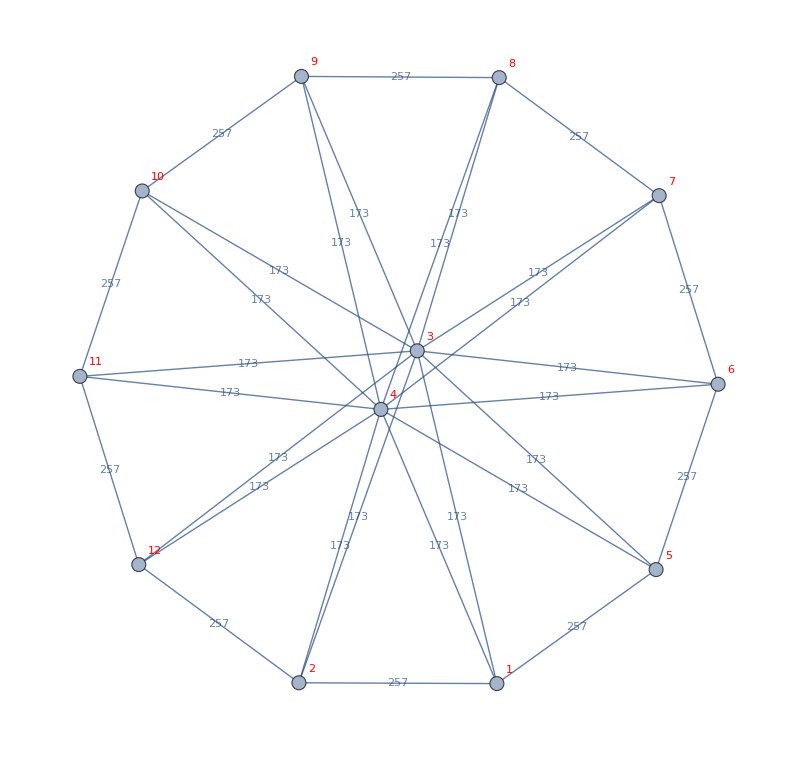

```mathematica
With[{
g=JacobsThalGraph[8]},
Graph[g,EdgeLabels->Table[e-> Weight[g,e],{e,EdgeList[g]}],VertexLabels->"Name",VertexLabelStyle->Red
]
]
```